# 09.26.2023 2D and 3D Plots in Mathematica Salizhan Kylychbekov

## 2D Plots

Plot::plln: Limiting value x_min in {x,x_min,x_max} is not a machine-sized real number.

Plot[f,{x,x_min,x_max}]

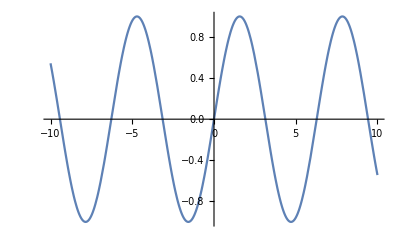

```mathematica
Plot[f, {x, Subscript[x, min], Subscript[x, max]}]
Plot[Sin[x],{x, -10, 10}]
```

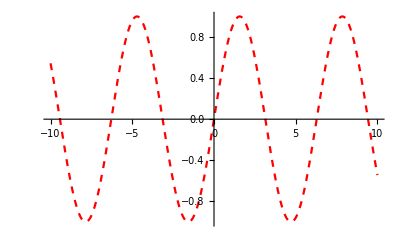

```mathematica
Plot[Sin[x],{x, -10, 10}, PlotStyle->{Red, Dashed}]
```

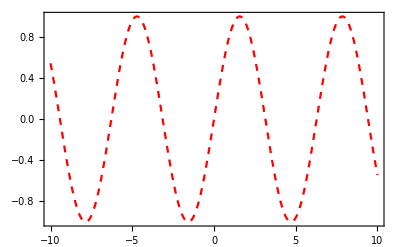

```mathematica
Plot[Sin[x],{x, -10, 10}, PlotStyle->{Red, Dashed}, AxesOrigin->{-7,0}, Frame->True]
```

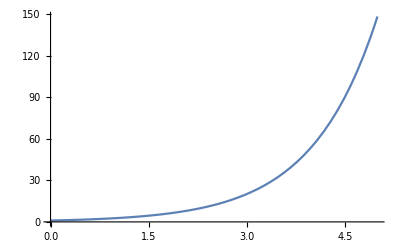

```mathematica
Plot[E^x, {x, 0, 5}]
```

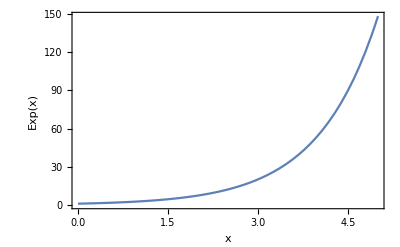

```mathematica
Plot[E^x, {x, 0, 5}, FrameLabel->{"x", "Exp(x)"},Frame->True, FrameStyle->Directive[Brown,Thick, 14]]
```

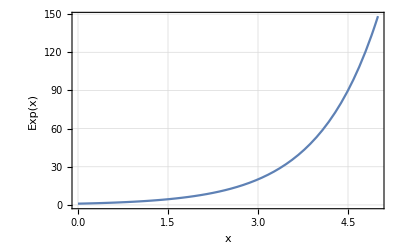

```mathematica
Plot[E^x, {x, 0, 5}, FrameLabel->{"x", "Exp(x)"},Frame->True, FrameStyle->Directive[Brown,Thick, 14], GridLines->Automatic]
```

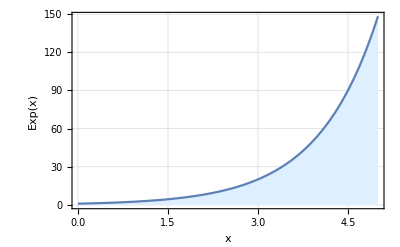

```mathematica
Plot[E^x, {x, 0, 5}, FrameLabel->{"x", "Exp(x)"},Frame->True, FrameStyle->Directive[Brown,Thick, 14], GridLines->Automatic, Filling-> Axis, FillingStyle-> LightBlue]
```

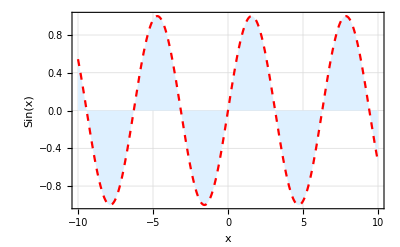

```mathematica
Plot[Sin[x], {x, -10, 10},PlotStyle->{Red, Dashed}, FrameLabel->{"x", "Sin(x)"},Frame->True, FrameStyle->Directive[Brown,Thick, 14], GridLines->Automatic, Filling-> Axis, FillingStyle-> LightBlue]
```

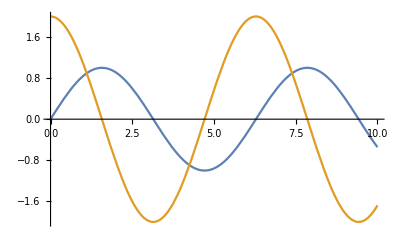

```mathematica
Plot[{Sin[x], 2Cos[x]},{x, 0, 10} ]
```

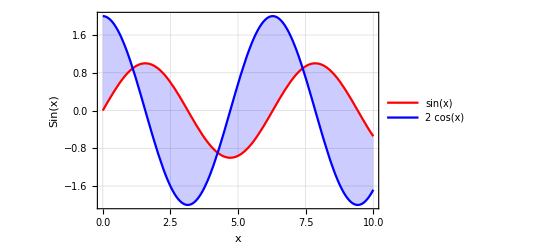

```mathematica
Plot[{Sin[x], 2Cos[x]},{x, 0, 10} , Filling->{1}, Axes->False, Frame->True, FrameLabel->{{"Sin(x)","2 Cos(x)"},{"x", "x"}}, PlotStyle->{Red, Blue}, GridLines->Automatic, PlotLegends->"Expressions", FrameStyle->Directive[Brown,Thick, 13]]
```

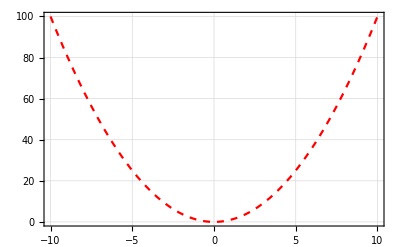

```mathematica
f[t_]:=t^2;
Plot[f[x],{x, -10, 10}, PlotStyle->{Red,Dashed},Frame->True,GridLines->Automatic, PlotLegends->"Expressions", FrameStyle->Directive[Brown,Thick, 13]]
```

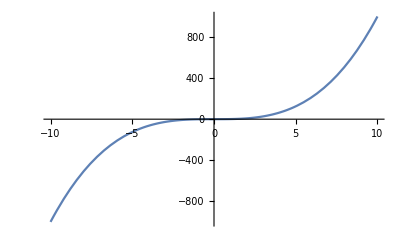

```mathematica
g[x]:=x^3;
Plot[g[x],{x, -10, 10}]
```

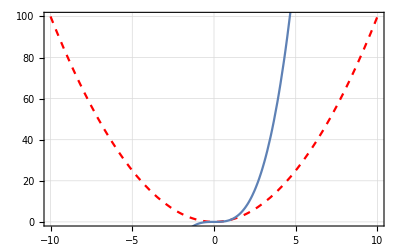

```mathematica
Show[%105, %96]
```

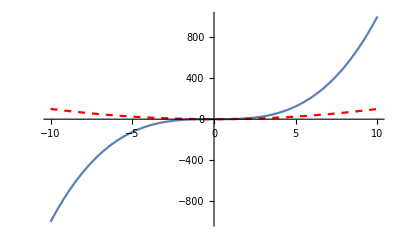

```mathematica
Show[%96, %105]
```